```mathematica
srcDir=NotebookDirectory[];
srcItem[filename_]:=FileNameJoin[{srcDir,filename}];
imgDir=FileNameJoin[{ParentDirectory[srcDir],"documentation-images"}];
imgItem[filename_]:=FileNameJoin[{imgDir,filename}];
```

```mathematica
img=Rasterize[
Import[imgItem["landsat.jpg"]],
ImageSize->1000
];
mesh=ImageMesh[img];
```

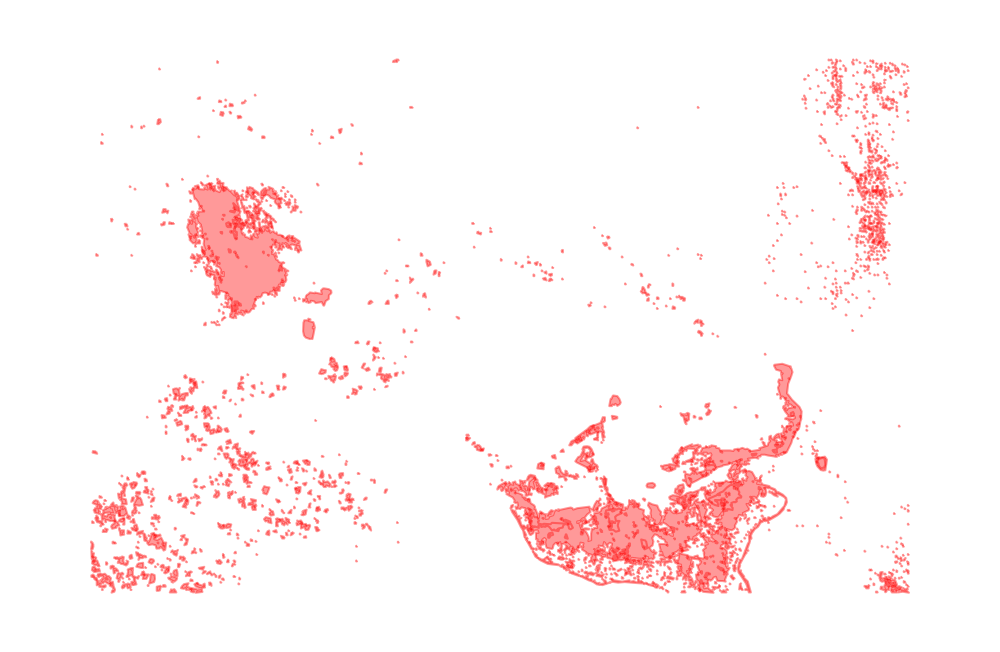

```mathematica
imgComp=GraphicsRow[{img,HighlightImage[img,mesh]},ImageSize->{Automatic,300},Spacings->0,Background->None]
```

```mathematica
|
```

```mathematica
Export[imgItem["landsat-output.png"],imgComp,Background->None];
```